```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../lib/lib2.m"];
Get["../lib/util.m"];
```

```mathematica
plotsDir= "../../plots/plots-104/";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
MeanData ={};
VarData ={};
Meanraw ={};
Varraw={};
Table[Module[{fn ,data,mns,vars,Kval,tdmns,tdval},
Kval =5;
fn = FileNames[All,"../../runs/Trials/N"<>ToString[Nval]<>"K"<>ToString[Kval]][[1;;3]];
Print[fn];

Print["Computing for N="<>ToString[Nval]];
data =Import[#]&/@fn;

Print["Changing N and K"];
changeNK[Nval,Kval];

matdata = cMat[#]&/@ data;

traces=Table[Tr[MatrixPower[#,n]]&/@matdata[[d]][[All,2]]//Chop//Re,{d,1,Length[matdata]},{n,5,8}];

mnsraw=Table[Mean[traces[[All,k]]//Transpose],{k,1,4}];

mns=Around[#]&/@mnsraw;

varsraw=Table[StandardDeviation[traces[[All,k]]//Transpose],{k,1,4}];

vars=Around[#]&/@varsraw;


AppendTo[Meanraw,mnsraw];
AppendTo[Varraw,varsraw];

tdmns=Thread[{Nval,#}]&/@mns;
tdval=Thread[{Nval,#}]&/@vars;
AppendTo[MeanData,tdmns];
AppendTo[VarData,tdval];

Export["MeanData2.dat",Meanraw];
Export["VarData2.dat",Varraw];
Print["Computing COMPLETE for N="<>ToString[Nval]];]
,{Nval,{3}}];

Print["Exporting data"];
```

{../../runs/Trials/N3K5\37797394.dat,../../runs/Trials/N3K5\37867891.dat,../../runs/Trials/N3K5\43467537.dat}

Computing for N=3

$Aborted

Exporting data

```mathematica
mnsraw
```

{{-0.000283307,-0.00148877,-0.00120336},{0.0244727,0.0240218,0.0185052},{-0.000237402,-0.000580753,-0.000697888},{0.00742488,0.00721989,0.0051697}}

```mathematica
Meanraw
```

{{{0.000234434,-0.000304893,0.00227123},{0.0179561,0.0167731,0.0269149},{0.000412464,-0.000325929,0.00217051},{0.00647771,0.00572263,0.0120497}},{{-0.000283307,-0.00148877,-0.00120336},{0.0244727,0.0240218,0.0185052},{-0.000237402,-0.000580753,-0.000697888},{0.00742488,0.00721989,0.0051697}}}

```mathematica
MeanData//Transpose
```

{{{3,0.00070.0014}},{{3,0.0210.006}},{{3,0.00080.0013}},{{3,0.00810.0035}}}

```mathematica
MeanData
```

{{{3,0.00070.0014},{3,0.0210.006},{3,0.00080.0013},{3,0.00810.0035}},{{5,-0.00100.0006},{5,0.02230.0033},{5,-0.000510.00024},{5,0.00660.0012}}}

```mathematica
Around[#]&/@mnsraw
```

{-0.00100.0006,0.02230.0033,-0.000510.00024,0.00660.0012}

```mathematica
VarData//Transpose
```

{{{3,0.0020.010},{5,0.00090.0034}},{{3,0.0000.005},{5,0.00020.0012}},{{3,0.0000.005},{5,0.00020.0012}}}

```mathematica
Print["Improting data"];
MeanData3to7 = Import["MeanData3to7.mx"];
VarData3to7= Import["VarData3to7.mx"];
MeanData89 = Import["MeanData89.mx"];
VarData89 = Import["VarData89.mx"];
MeanData = Join[MeanData3to7,MeanData89];
VarData = Join[VarData3to7,VarData89];
```

Improting data

```mathematica
MeanData//Length
```

7

```mathematica
Around[VarData[[1,4]]]//N[#, 10]&
```

0.0050.005

```mathematica
StandardDeviation[%14]//N
```

0.00541011

```mathematica
Mean[%14]//N
```

0.00475624

```mathematica
%18-%17
```

-0.000653869

```mathematica
And@@Positive[MeanData[[1,4]]]
```

True

```mathematica
MeanData[[1,4]]//Around
```

0.00100.0008

```mathematica
mpdata = Table[Thread[{Nval,#}]&/@(Around[#]&/@MeanData[[Nval-2]]),{Nval,3,9}];
mstpdata = Table[Thread[{Nval,#}]&/@(Around[#]&/@VarData[[Nval-2]]),{Nval,3,9}];
```

```mathematica
xval ={5,6,7,8}
```

{5,6,7,8}

```mathematica
(mpdata//Transpose)[[1]]
```

{{3,0.00.9},{4,-0.020.34}}

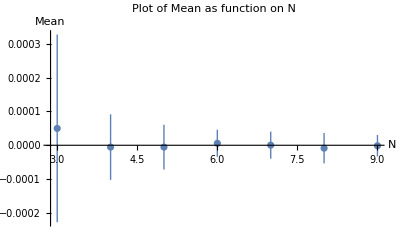
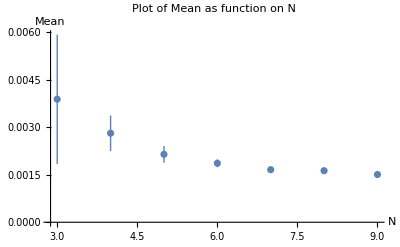
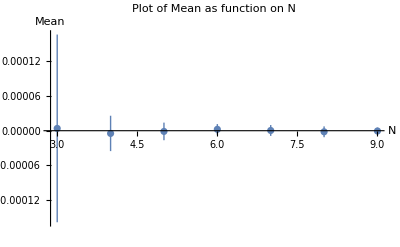
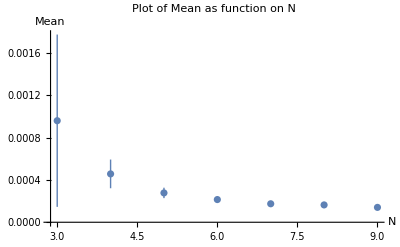

```mathematica
Table[ListPlot[(mpdata//Transpose)[[k]],PlotLabel->"Plot of Mean as function on N",PlotRange->All,PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[\!\(\*SuperscriptBox[\(X\),n]\)]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Mean"}],{k,1,4}]
```

```mathematica
Print["Plotting"];
pltmnsdiff=GraphicsGrid[ArrayReshape[Table[ListPlot[(mpdata//Transpose)[[k]],PlotLabel->"Tr[(X^1)^n]; n = "<>ToString[xval[[k]]],PlotRange->{All,{-0.003,0.008}},AxesLabel->{"N","Mean"}],{k,1,4}],{2,2}],ImageSize->Full];
pltmns=ListPlot[(mpdata//Transpose),PlotLabel->"Plot of Mean as function on N",PlotRange->All,PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[(X^1)^n]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Mean"},ImageSize->Full];
```

Plotting

```mathematica
Print["Plotting"];
pltvarsdiff=GraphicsGrid[ArrayReshape[Table[ListPlot[(mstpdata//Transpose)[[k]],PlotLabel->"Tr[(X^1)^n]; n = "<>ToString[xval[[k]]],PlotRange->{All,{-0.003,0.02}},AxesLabel->{"N","StandardDeviation"}],{k,1,4}],{2,2}]];
pltvars=ListPlot[(mstpdata//Transpose),PlotLabel->"Plot of StandardDeviation as function on N",PlotRange->All,PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[(X^1)^n]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Standard Deviation"},ImageSize->Full];
```

Plotting

```mathematica
Print["Exporting Plots"];
Export[plotsDir<>"/Plot_of_Means.pdf",pltmns,ImageResolution->300,ImageSize->500];
Export[plotsDir<>"/Plot_of_Vars.pdf",pltvars,ImageResolution->300,ImageSize->500];
Export[plotsDir<>"/Plot_of_Meansdiff.pdf",pltmnsdiff,ImageResolution->300,ImageSize->500];
Export[plotsDir<>"/Plot_of_Varsdiff.pdf",pltvarsdiff,ImageResolution->300,ImageSize->500];
```

Exporting Plots

```mathematica
Print["Program Completed"];
```

## Log Plot

Plotting

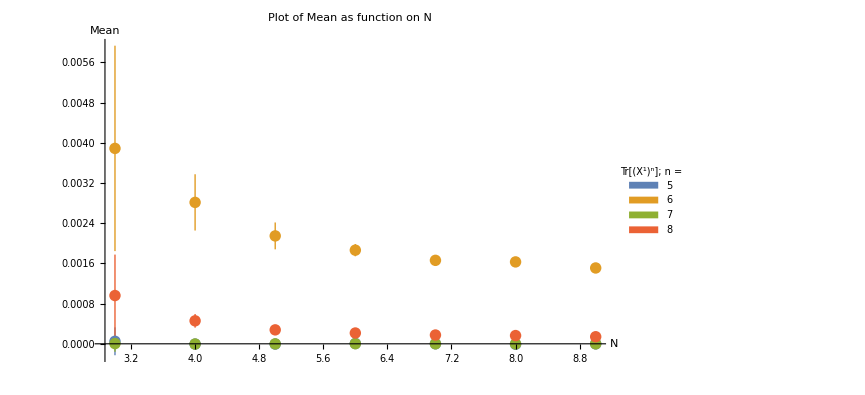

```mathematica
Print["Plotting"];
pltmnsdiff=GraphicsGrid[ArrayReshape[Table[ListLogPlot[(mpdata//Transpose)[[k]],PlotLabel->"Tr[(X^1)^n]; n = "<>ToString[xval[[k]]],PlotRange->{All,{-0.003,0.008}},AxesLabel->{"N","Mean"}],{k,1,4}],{2,2}],ImageSize->Full];
pltmns=ListPlot[(mpdata//Transpose),PlotLabel->"Plot of Mean as function on N",PlotRange->{All,All},PlotLegends->SwatchLegend[Automatic,xval,LegendLabel->Placed["Tr[(X^1)^n]; n = ",Above],LegendFunction->"Frame"],AxesLabel->{"N","Mean"}]
```